```mathematica
ClearAll[f]
```

```mathematica
f[x_]:=Sin[x ^ 2] + 1.5;
start = 0;
end = 2 * Pi;
numberOfParts = 10;
xValues := Range[start, end, (end-start)/(numberOfParts)];
yValues := Map[f,xValues];
```

```mathematica
functionPlot := Plot[f[x], {x, start, end}, Filling->Axis, PlotRange->{{start, end},{0, 2.5}}]
```

```mathematica
riemannLeft[x_] := yValues[[x]]
```

```mathematica
riemannRight[x_] := yValues[[x + 1]]
```

```mathematica
riemannMean[x_] := (yValues[[x]] + yValues[[x + 1]]) / 2
```

```mathematica
riemannMode[x_] := riemannMean[x]
riemannColumns := Table[
	Module[{xStart, xEnd, yCurrent},
		xStart = xValues[[x]];
		xEnd = xValues[[x+1]];
		yCurrent = riemannMode[x];
		Graphics[{
			Red,
			Polygon[{{xStart, 0}, {xStart, yCurrent}, {xEnd, yCurrent}, {xEnd, 0}}]
		}]
	],
	{x, 1, Length[xValues] - 1}
]
riemannArea := Sum[
	(xValues[[x + 1]] - xValues[[x]]) * riemannMode[x],
	{x, 1, Length[xValues] - 1}
]
riemannAreaText := "Riemann area: " <> ToString[riemannArea // N]
```

```mathematica
Sum[
	(xValues[[x + 1]] - xValues[[x]]) * riemannMode[x],
	{x, 1, Length[xValues] - 1}
] // N
```

9.35673

```mathematica
actualArea := NIntegrate[f[x],{x, start, end}]
actualAreaText := "Actual area: " <> ToString @ actualArea
```

```mathematica
error := Abs[actualArea - riemannArea]
errorText := "Error: " <> ToString[error // N]
```

```mathematica
Manipulate[
	numberOfParts = a;
	Grid[{
			{
				Show @ Flatten[{functionPlot, riemannColumns, functionPlot}]
			},
			{
				actualAreaText
			},
			{
				riemannAreaText
			},
			{
				errorText
			}
		}],
	{a,1,50,1}
]
```

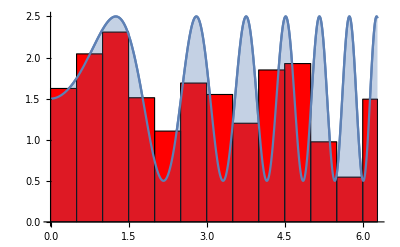
-Graphics-
Riemann area: 9.58697
Actual area: 10.0669

```mathematica
riemannGraphic[function_, start_, end_, rectWidth_] := Module[
{bars, plot, actualArea, riemannArea},
	riemannArea = 0;
	bars = Table[
		Module[{xStart, xEnd, yCurrent},
			xStart = start + (rectWidth * (x - 1));
			xEnd = Min[xStart + rectWidth, end]; 
			yCurrent = (function[xStart] + function[xEnd]) / 2.;
			riemannArea = riemannArea + ((xEnd - xStart) * yCurrent);
			Graphics[{
				EdgeForm[{Thick, Black}],
				Red,
				Polygon[{{xStart, 0}, {xStart, yCurrent}, {xEnd, yCurrent}, {xEnd, 0}}]
			}]
		],
		{x, 1, Ceiling[(end - start) / rectWidth]}
	];
	plot = Plot[f[x], {x, start, end}, Filling->Axis, PlotRange->{{start, end},{0, 2.5}}];
	actualArea = NIntegrate[function[x], {x, start, end}];
	Grid[{
		{
			Show @ Flatten[{plot, bars, plot}]
		},
		{
			"Riemann area: " <> ToString @ riemannArea
		},
		{
			"Actual area: " <> ToString @ actualArea
		}
	}]
]
bars = riemannGraphic[Sin[#^2] + 1.5&, 0, 2*Pi, 0.5]
```

```mathematica
2 * Pi // N
```

6.28319

```mathematica
(*From downloaded document*)
Manipulate[
Module[{plotpoint,grect,integrate,i},
plotpoint=Table[{x,f[x]},{x,1,5,1/2^n}];
grect[i_]:=Switch[cont,"right",yaf[i,plotpoint],"left",ybe[i,plotpoint],"max",ymax[i,plotpoint],"min",ymin[i,plotpoint],"mean",ymean[i,plotpoint]];
integrate[i_]:=Switch[cont,"right",af[n,i,plotpoint],"left",be[n,i,plotpoint],"max",max[n,i,plotpoint],"min",min[n,i,plotpoint],"mean",mean[n,i,plotpoint]];
Grid[{{
Show[
Graphics[
Table[{Hue[j/Length[plotpoint]],grect[j]},{j,1,Length[plotpoint]-1}],
Axes->True,
PlotRange->{{0.5,5.5},{0,3}},
AspectRatio->3/5,
GridLines->Automatic
],
ImageSize->{500,300}
]
}}
]
],
{{n,1,"subdivision multiplier n"},1,8,1,Appearance->"Labeled"},{{cont,"mean","rectangle heights"},{"left","right","max","min","mean"},ControlType->PopupMenu},SaveDefinitions->True,AutorunSequencing->{2,{1,8}}
]
```